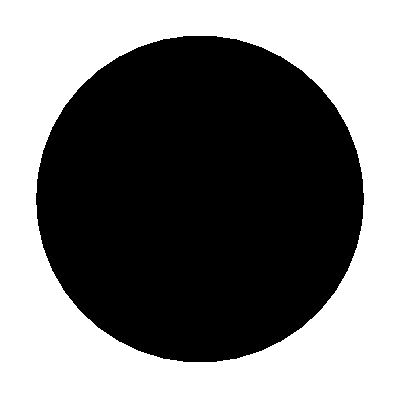

/home/eduard/programming/Evolutionary/src/test/resources/physics/ball.obj

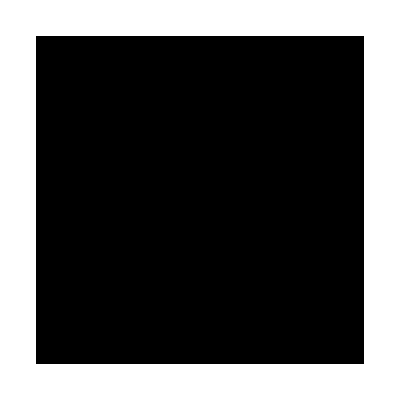

/home/eduard/programming/Evolutionary/src/test/resources/physics/square.obj

```mathematica
ExportMesh[file_,region_,measure_]:=Module[{r,c,in},
r=DiscretizeRegion[region,MaxCellMeasure->measure];
c=MeshCells[r,2];
in=MeshCoordinates[r];
Print[Graphics[c/.i_Integer:> in[[i]]]];
Export[file, r]
]

ExportMesh["/home/eduard/programming/Evolutionary/src/test/resources/physics/ball.obj",Disk[],0.1]
ExportMesh["/home/eduard/programming/Evolutionary/src/test/resources/physics/square.obj",Polygon[{{0,0},{1,0},{1,1},{0,1}}],0.01]
```